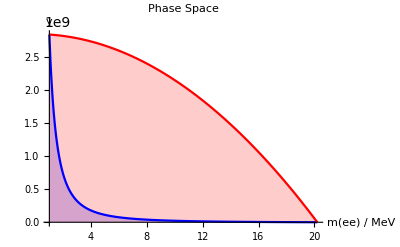

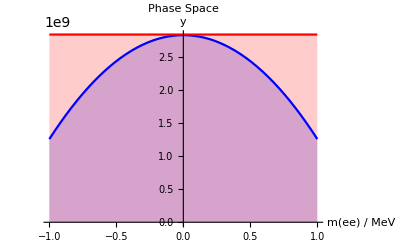

2.84544×10^9

```mathematica
Plot[{mtest[q,1.],mtest[q,0.]},                   {q,qmin,qmax},
PlotLabel->"Phase Space",
FrameLabel->{"q/MeV","dPS/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue,Red}
]
Plot[{mtest[2*me*1.5,c],mtest[2*me,c]},                   {c,-1.,1.},
PlotLabel->"Phase Space",
FrameLabel->{"q/MeV","dPS/dq"},
PlotRange->{{-1,1},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue,Red}
]
mtest[2*me,0.]
```

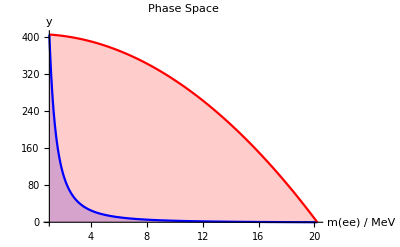

```mathematica
mee[q_,cos_]:=m^2-m3^2-2*m*(m^2-m3^2+q^2)/(2*m)+4*e1[q,cos]*e2[q,cos];
Plot[{mee[q,1.],mee[q,0.]},                   {q,qmin,qmax},
PlotLabel->"Phase Space",
FrameLabel->{"q/MeV","dPS/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue,Red}
]
```

```mathematica
mee[2*me,1.]
```

405.206

```mathematica
qmin
```

0.0001022

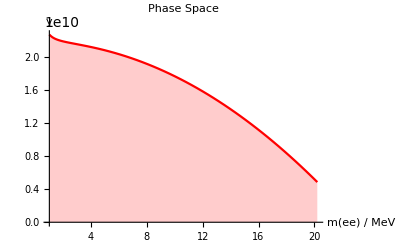

```mathematica
mm[q_]:=(m^2-m3^2-q^2)^2-(2/3)(m/q)^2(((m^2-m3^2+q^2)/(2m))^2-q^2)(q^2/4-me^2)-Pi m3^2q^2;
Plot[{mm[q]},                   {q,qmin,qmax},
PlotLabel->"Phase Space",
FrameLabel->{"q/MeV","dPS/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue,Red}
]
```

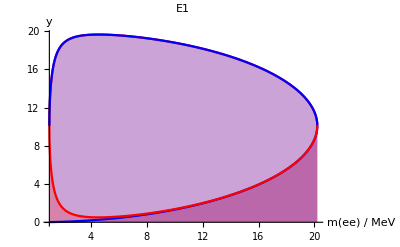

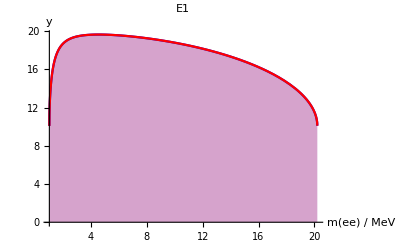

```mathematica
pem[q_,cos_]:=q/2(gamma[q](cos+vel[q]));
Eem[q_,cos_]:=q/2(gamma[q](1-cos*vel[q]));
Plot[{Sqrt[Eem[q,1.]^2],e11[q,1.],e1[q,1.],e1min[q]},                   {q,qmin,qmax},
PlotLabel->"E1",
FrameLabel->{"q/MeV","dPS/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue,Red}
]
Plot[{e1[q,1.],e11[q,1.]},                   {q,qmin,qmax},
PlotLabel->"E1",
FrameLabel->{"q/MeV","dPS/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue,Red}
]
```

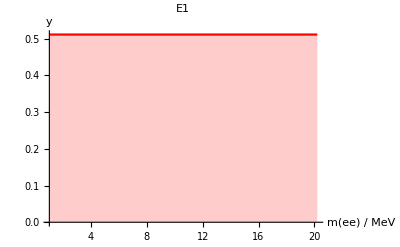

```mathematica
Plot[{Sqrt[e1[q,0]^2-p1z[q,0.]^2-p1x[q,0.]^2]},                   {q,qmin,qmax},
PlotLabel->"E1",
FrameLabel->{"q/MeV","dPS/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue,Red}
]
```

```mathematica
mtest[q_,cos_]:=2*p3p1[q,cos]*p3p2[q,cos]-m3^2*q^2/2. ;
mtesti[q_]:=Integrate[mtest[q,c],{c,-1,1}];
```

408.444

1.022

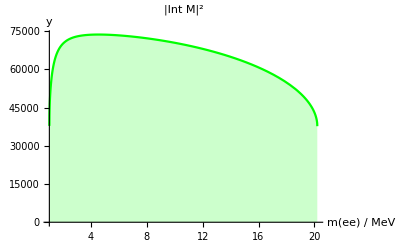

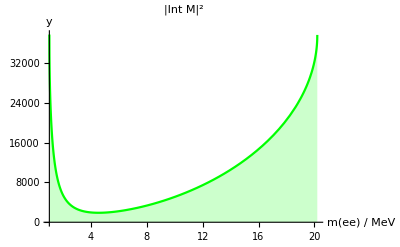

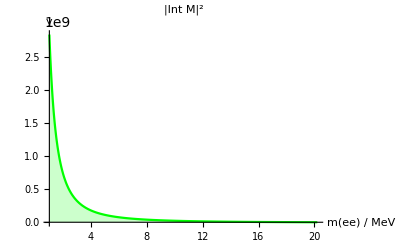

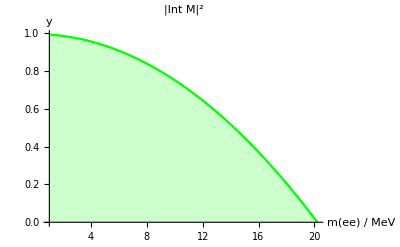

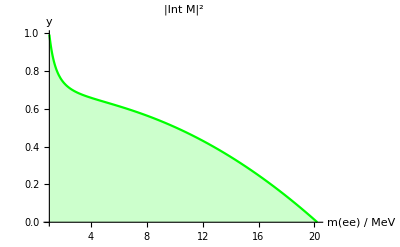

-Graphics-

```mathematica
q2max
qmin
cs=1.;
Plot[p3p1[q,cs],                   {q,qmin,qmax},
PlotLabel->"|Int M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,2},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Green}
]
Plot[p3p2[q,cs],                   {q,qmin,qmax},
PlotLabel->"|Int M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,2},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Green}
]
Plot[2 p3p1[q,cs]*p3p2[q,cs]-m3^2*q^2/2,                   {q,qmin,qmax},
PlotLabel->"|Int M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,2},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Green}
]
Plot[me2[q]/m^2/q2max,                   {q,qmin,qmax},
PlotLabel->"|Int M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Green}
]
Plot[mtesti[q]/m^2/q2max,                   {q,qmin,qmax},
PlotLabel->"|Int M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Green}
]
Plot[mme1[q]/m^2/q2max,                   {q,qmin,qmax},
PlotLabel->"|Int M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Green}
]
```

```mathematica
qmin
qmax
Clear[q]
qmi=2*me
e3[qmi]
p3[qmi]
e1s[qmi]
e1min[qmi]
e1max[qmi]
```

1.022

20.21

1.022

3727.43

20.1297

0.510999

10.0778

10.0778

```mathematica
Integrate[(a1+b1 *Cos[x]+c1 *Sin[x]+d1 *Cos[x]^2)*Sin[x],{x,0.,Pi}]
```

0.+2. a1+1.5708 c1+0.666667 d1

```mathematica
mtesti[q]
me2[q]
```

3.81918×10^9+(1.96517×10^9)/q^2-(1.98682×10^-8)/q+2.62462×10^-9 q-9.36228×10^6 q^2-4.57723×10^-15 q^3-0.160421 q^4-3.31486×10^-23 q^5+1.7673×10^-8 q^6-2.11242×10^-16 q^8+99364.4 √(-0.26112+q^2/4) √(-1.04448+q^2)-(4.0694×10^7 √(-0.26112+q^2/4) √(-1.04448+q^2))/q^2+0.654175 q^2 √(-0.26112+q^2/4) √(-1.04448+q^2)-3.5346×10^-8 q^4 √(-0.26112+q^2/4) √(-1.04448+q^2)+4.22484×10^-16 q^6 √(-0.26112+q^2/4) √(-1.04448+q^2)

2 (-6.94668×10^6 q^2+1/8 (151069.-q^2)^2)

```mathematica
Integrate[Sin[x],{x,0,Pi}]
```

2

```mathematica
mtest[x,y]
```

-6.94668×10^6 x^2+2 (0.000133419 (2.79378×10^7-x^2) (0.0000667095 (151069.+x^2)-(0.0000667095 √(-1.04448+x^2) √((1.40444×10^7-(3727.38-x)^2) (1.40444×10^7-(3727.38+x)^2)) y)/x)+0.000133419 √((1.40444×10^7-(3727.38-x)^2) (1.40444×10^7-(3727.38+x)^2)) (0.0000667095 √((1.40444×10^7-(3727.38-x)^2) (1.40444×10^7-(3727.38+x)^2))-(√(-0.26112+x^2/4) (3747.59-0.000133419 (2.79378×10^7-x^2)) y)/x)) (0.000133419 (2.79378×10^7-x^2) (0.0000667095 (151069.+x^2)+(0.0000667095 √(-1.04448+x^2) √((1.40444×10^7-(3727.38-x)^2) (1.40444×10^7-(3727.38+x)^2)) y)/x)+0.000133419 √((1.40444×10^7-(3727.38-x)^2) (1.40444×10^7-(3727.38+x)^2)) (0.0000667095 √((1.40444×10^7-(3727.38-x)^2) (1.40444×10^7-(3727.38+x)^2))+(√(-0.26112+x^2/4) (3747.59-0.000133419 (2.79378×10^7-x^2)) y)/x))

```mathematica
m3^2/2
```

6.94668×10^6

```mathematica
qs=qmax;
cs=1.;
e1[qs,cs]+e2[qs,cs]+e3[qs]-m
Sqrt[e1[qs,cs]^2-p1z[qs,cs]^2-p1x[qs,cs]^2]
p3[qs]-p1z[qs,cs]-p2z[qs,cs]
p3p1[qs,cs]
p3p2[qs,cs]
2p3p1[qs,cs]p3p2[qs,cs]
m3^2*qs^2/2.
2p3p1[qs,cs]p3p2[qs,cs]-m3^2*qs^2/2.
```

6.50147×10^-13

0.510999

0.

37665.2

37665.2

2.83733×10^9

2.83733×10^9

0.0000553131

```mathematica
a=qmax;
b=1.;
p32=m3*(m-m3)/2;
(2 p3p1[a,b]*p3p2[a,b]-m3^2*a^2/2)*10^7
(2*p32*p32                             -m3^2*a^2/2)*10^7
2 p3p1[a,b]*p3p2[a,b]
2 p32 p32                                  
m3^2*a^2/2
```

553.131

4.76837

2.83733×10^9

2.83733×10^9

2.83733×10^9

```mathematica
a=qmin;
b=1.;
p32=(m^2-m3^2+qmin^2)/(4m)*(m^2+m3^2-qmin^2)/(2m)+Sqrt[((m^2-m3^2+qmin^2)/(4m))^2-me^2]*Sqrt[((m^2+m3^2-qmin^2)/(2m))^2-m3^2];
(2 p3p1[a,b]*p3p2[a,b]-m3^2*a^2/2)
(2*p32*p32                             -m3^2*a^2/2)
mtest[a,b]
2 p3p1[a,b]*p3p2[a,b]
2 p32 p32                                  
m3^2*a^2/2
```

2.84544×10^9

2.84544×10^9

2.84544×10^9

2.8527×10^9

2.8527×10^9

7.25567×10^6